{980.45,-415.8,54.8,-14.64,-14.64}

4

4

{{4,4}}

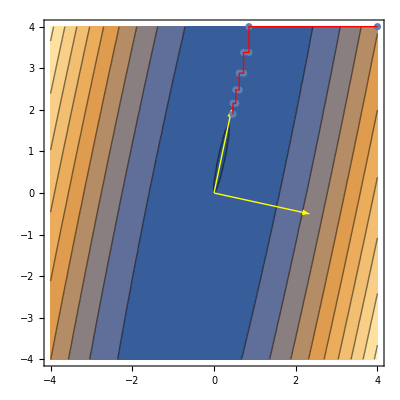

```mathematica
{Subscript[a, 1], Subscript[a, 2], Subscript[a, 3], Subscript[b, 1],Subscript[b, 2]}={980.45, -415.8,54.8, -14.64, -14.64}
f[x1_, x2_]:=Subscript[a, 1] x1^2+Subscript[a, 2] x1 x2+Subscript[a, 3] x2^2+Subscript[b, 1] x1+Subscript[b, 2] x2
x1=4
x2=4
xs={{x1, x2}}
For[ i =0, i<5, i++,
x1=(-x2 Subscript[a, 2]-Subscript[b, 1])/(2 Subscript[a, 1]);
AppendTo[xs, {x1, x2}];
x2=(-x1 Subscript[a, 2]-Subscript[b, 2])/(2 Subscript[a, 3]);
AppendTo[xs, {x1, x2}];
]
Show[ContourPlot[f[Subscript[x, 1], Subscript[x, 2]], {Subscript[x, 1], -4, 4}, {Subscript[x, 2],-4, 4}],ListPlot[xs], 
Graphics[{Thick, Yellow, Arrow[{{0, 0},-{-4.666666666666667,1}/2}]}],
Graphics[{Thick, Yellow, Arrow[{{0, 0},{0.21428571428571455,1}*2}]}],Graphics[{Thick, Red, Line[xs]}]]
```

```mathematica
xs
```

{{4,4},{0.855648,4},{0.855648,3.37973},{0.724122,3.37973},{0.724122,2.88075},{0.618316,2.88075},{0.618316,2.47934},{0.533199,2.47934},{0.533199,2.15642},{0.464726,2.15642},{0.464726,1.89665}}

```mathematica
Fx1[x1_, x2_,alpha_,x01_,x02_]:=-((2 Cos[alpha] (x01-x2 Sin[alpha]) Subscript[a, 1]+(x02 Cos[alpha]+x2 Cos[2 alpha]+x01 Sin[alpha]) Subscript[a, 2]+Cos[alpha] Subscript[b, 1]+Sin[alpha] (2 (x02+x2 Cos[alpha]) Subscript[a, 3]+Subscript[b, 2]))/(2 (Cos[alpha]^2 Subscript[a, 1]+Sin[alpha] (Cos[alpha] Subscript[a, 2]+Sin[alpha] Subscript[a, 3]))));
Fx2[x1_, x2_]:=(2 (x01+x1 Cos[alpha]) Sin[alpha] Subscript[a, 1]-(x01 Cos[alpha]+x1 Cos[2 alpha]-x02 Sin[alpha]) Subscript[a, 2]+Sin[alpha] Subscript[b, 1]-Cos[alpha] (2 (x02+x1 Sin[alpha]) Subscript[a, 3]+Subscript[b, 2]))/(2 (Sin[alpha]^2 Subscript[a, 1]+Cos[alpha] (-Sin[alpha] Subscript[a, 2]+Cos[alpha] Subscript[a, 3])));
```

```mathematica
{Subscript[a, 1], Subscript[a, 2], Subscript[a, 3], Subscript[b, 1],Subscript[b, 2]}={980.45, -415.8,54.8, -14.64, -14.64}
f[x1_, x2_]:=Subscript[a, 1] x1^2+Subscript[a, 2] x1 x2+Subscript[a, 3] x2^2+Subscript[b, 1] x1+Subscript[b, 2] x2
x1=4
x2=4
x1new=x1;
x2new=x2;
alpha=0;
xs={{x1, x2}}
x01=0;
x02=0;
For[ i =0, i<5, i++,
x1=Fx1[x1new, x2new,alpha,x1,x2];
AppendTo[xs, {x1, x2}];
x2=Fx2[x1new, x2new,alpha,x1,x2];
AppendTo[xs, {x1, x2}];
alpha=ArcTan[(xs[[Length@xs,2]]-xs[[Length@xs-2,2]])/(xs[[Length@xs,1]]-xs[[Length@xs-2,1]])];
x1new=0;
x2new=0;
]
Show[ContourPlot[f[Subscript[x, 1], Subscript[x, 2]], {Subscript[x, 1], -4, 4}, {Subscript[x, 2],-4, 4}],ListPlot[xs], 
Graphics[{Thick, Yellow, Arrow[{{0, 0},-{-4.666666666666667,1}/2}]}],
Graphics[{Thick, Yellow, Arrow[{{0, 0},{0.21428571428571455,1}*2}]}],Graphics[{Thick, Red, Line[xs]}]]
```

{980.45,-415.8,54.8,-14.64,-14.64}

4

4

{{4,4}}

-Graphics-

```mathematica
xs
```

{{4,4},{Fx1[4,4,0,4,4],4},7,{Fx1[0,3,Fx2[0,0,ArcTan[1],Fx1[1],Fx2[0,3,Fx2[0,0,ArcTan[(-4+Fx2[4,3,4])/(-4+Fx1[4,4,0,4,4])],Fx1[0,0,ArcTan[(-4+Fx2[4,4,0,Fx1[4,4,0,4,4],4])/(-4+Fx1[4,4,0,4,4])],Fx1[4,4,0,4,4],Fx2[4,4,0,Fx1[4,4,0,4,4],4]],Fx2[4,4,0,Fx1[4,4,0,4,4],4]]]]],1},1}
 |  |  |  |